```mathematica
(* Initialization *)
SetOptions[EvaluationNotebook[],Background->Lighter@Lighter@Orange]
```

# Úkol 1 Jan Smrža

Naprogramovat 3 různé řadící algoritmy.
1x O(n2) (ne Bubble sort)
2x O(n*log(n)) (ne Quick sort)
Ověřit čas potřebný pro seřazení pole stejných náhodných čísel o rozměru 10, 100,1000,10000,100000 prvků.
Ověřit čas potřebný pro seřazení seřazeného pole čísel o velikosti 10, 100,1000,10000,100000 prvků.
Ověřit čas potřebný pro seřazení obráceně seřazeného pole čísel o velikosti 10, 100,1000,10000,100000 prvků.
Porovnat teoretickou složitost algoritmů s naměřenými výsledky pomocí tabulek a grafů.
Srovnejte naměřené časy s vestavěnou funkcí Sort[] (odhadněte jaká je průměrná časová složitost funkce Sort[]).
Výsledný report bude obsahovat slovní závěr, ve kterém zodpovíte následující otázky:
Jaký třídící algoritmus byl nejrychlejší?
Mají nějakou výhodu algoritmy s časovou složitostí O(n2) ?

Zdrojové kódy

```mathematica
dataTest = RandomInteger[{0,10}, 10]
```

{9,7,5,8,8,10,8,6,3,3}

```mathematica
(* n^2 selectionsort *)
```

```mathematica
SelectionSort[arrInput_] := Module[{arr=arrInput, i, j, minIndex, tmp},
For[i= 1, i ≤ Length@arr  - 1, i++,
minIndex = Length@arr;
For[j = i, j ≤ Length@arr, j++,
If[arr[[minIndex]]>arr[[j]],
minIndex = j;
];
];
tmp = arr[[minIndex]];
arr[[minIndex]] = arr[[i]];
arr[[i]] = tmp;
];
Return@arr;
]
```

```mathematica
SelectionSort@dataTest
```

{3,3,5,6,7,8,8,8,9,10}

```mathematica
(* n*log(n) heapsort *)
```

```mathematica
HeapHelper[inp_,end_,start_]:=Module[{output = inp,root = start,value,child},
value=output[[root]];
child=root*2;

If[child<end&&output[[child]]>output[[child+1]],
child++
];

While[child≤end&&value>output[[child]],
output[[root]]=output[[child]];
root=child;
child=child*2;

If[child<end&&output[[child]]>output[[child+1]],
child++];
];

output[[root]]=value;

Return@output;
];

HeapSort[inp_]:=Module[{output = inp,length,i},
length=Length@output;

For[i=length/2,i≥1,i--,
output=HeapHelper[output,length,i];
];

For[i=length,i≥1,i--,
{output[[1]],output[[i]]}={output[[i]],output[[1]]};
output=HeapHelper[output,i-1,1];
];

Return@Reverse[output];
];
```

```mathematica
HeapSort@dataTest
```

{3,3,5,6,7,8,8,8,9,10}

```mathematica
(* n*log(n) mergesort *)
```

```mathematica
MergeSort[array_]:=Module[{left, middle, right,i = 1,j = 1,output = {}},
If[Length@array≤1, 
Return@array
];

middle=Round[Length@array/2];
left=MergeSort[array[[1;;middle]]];
right=MergeSort[array[[middle+1;;-1]]];

While[i<=Length@left && j<=Length@right,
If[left[[i]]<right[[j]],
AppendTo[output,left[[i]]];
i++,
AppendTo[output,right[[j]]];
j++;
];
];

While[i≤Length@left,
AppendTo[output,left[[i]]];
i++;
];

While[j≤Length@right,
AppendTo[output,right[[j]]];
j++;
];

Return@output
]
```

```mathematica
MergeSort@dataTest
```

{3,3,5,6,7,8,8,8,9,10}

```mathematica
data=Table[RandomInteger[{1,100},n],{n,{10,100, 1000, 10000, 100000}}];
```

```mathematica
dataSorted = Join[{Sort[data[[1]]]}, {Sort[data[[2]]]}, {Sort[data[[3]]]}, {Sort[data[[4]]]}, {Sort[data[[5]]]}];
dataReverse = Join[{Reverse[dataSorted[[1]]]}, {Reverse[dataSorted[[2]]]}, {Reverse[dataSorted[[3]]]}, {Reverse[dataSorted[[4]]]}, {Reverse[dataSorted[[5]]]}];
```

```mathematica
tabulka[results_]:=Module[{},
Grid[{
{"10","100", "1000", "10000", "100000"},
{results[[1]],results[[2]], results[[3]], results[[4]], results[[5]]}},
Frame->All]
]
```

Výsledky

```mathematica
resultsSelection=
Table[
Mean[
Table[
AbsoluteTiming[
SelectionSort@d] [[1]],{1}]
]
,{d,data}];

resultsSelectionSorted=
Table[
Mean[
Table[
AbsoluteTiming[
SelectionSort@d] [[1]],{1}]
]
,{d,dataSorted}];

resultsSelectionReverse=
Table[
Mean[
Table[
AbsoluteTiming[
SelectionSort@d] [[1]],{1}]
]
,{d,dataReverse}];

resultsMerge=
Table[
Mean[
Table[
AbsoluteTiming[
MergeSort@d] [[1]],{1}]
]
,{d,data}];

resultsMergeSorted=
Table[
Mean[
Table[
AbsoluteTiming[
MergeSort@d] [[1]],{1}]
]
,{d,dataSorted}];

resultsMergeReverse=
Table[
Mean[
Table[
AbsoluteTiming[
MergeSort@d] [[1]],{1}]
]
,{d,dataReverse}];

resultsHeap=
Table[
Mean[
Table[
AbsoluteTiming[
HeapSort@d] [[1]],{1}]
]
,{d,data}];

resultsHeapSorted=
Table[
Mean[
Table[
AbsoluteTiming[
HeapSort@d] [[1]],{1}]
]
,{d,dataSorted}];

resultsHeapReverse=
Table[
Mean[
Table[
AbsoluteTiming[
HeapSort@d] [[1]],{1}]
]
,{d,dataReverse}];

resultsSort=
Table[
Mean[
Table[
AbsoluteTiming[
Sort@d] [[1]],{1}]
]
,{d,data}];

resultsSortSorted=
Table[
Mean[
Table[
AbsoluteTiming[
Sort@d] [[1]],{1}]
]
,{d,dataSorted}];

resultsSortReverse=
Table[
Mean[
Table[
AbsoluteTiming[
Sort@d] [[1]],{1}]
]
,{d,dataReverse}];
```

Tabulky a Grafy

```mathematica
tableSelection= tabulka[resultsSelection]
tableSelectionSorted= tabulka[resultsSelectionSorted]
tableSelectionReverse= tabulka[resultsSelectionReverse]
```

```mathematica
(* Selection s náhodným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0004206 | 0.0116479 | 0.844808 | 127.07 | 11202.9

```mathematica
(* Selection se seřazeným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0002019 | 0.0114619 | 1.08559 | 109.567 | 11139.

```mathematica
(* Selection se seřazeným převráceným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0002062 | 0.0111255 | 1.07242 | 110.857 | 11196.2

```mathematica
tableHeap= tabulka[resultsHeap]
tableHeapSorted= tabulka[resultsHeapSorted]
tableHeapReverse= tabulka[resultsHeapReverse]
```

```mathematica
(* HeapSort s náhodným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0002766 | 0.0045843 | 0.0731538 | 1.03461 | 12.5399

```mathematica
(* HeapSort se seřazeným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.00031 | 0.0060254 | 0.0838072 | 0.971815 | 11.7443

```mathematica
(* HeapSort se seřazeným převráceným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0002382 | 0.0044393 | 0.065397 | 0.915841 | 11.6738

```mathematica
tableMerge= tabulka[resultsMerge]
tableMergeSorted= tabulka[resultsMergeSorted]
tableMergeReverse= tabulka[resultsMergeReverse]
```

```mathematica
(* MergeSort s náhodným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0006899 | 0.0071885 | 0.0876419 | 1.43382 | 53.0804

```mathematica
(* MergeSort se seřazeným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0006056 | 0.0066213 | 0.0834081 | 1.3288 | 51.7801

```mathematica
(* MergeSort se seřazeným reverse vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
0.0006092 | 0.0065556 | 0.083591 | 1.31032 | 51.4353

```mathematica
tableSort= tabulka[resultsSort]
tableSortSorted= tabulka[resultsSortSorted]
tableSortReverse= tabulka[resultsSortReverse]
```

```mathematica
(* Sort Mathematica s náhodným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
6.4×10^-6 | 7.×10^-6 | 0.0000685 | 0.0007094 | 0.0080593

```mathematica
(* Sort Mathematica se seřazeným vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
2.4×10^-6 | 2.×10^-6 | 6.4×10^-6 | 0.0000472 | 0.0003454

```mathematica
(* Sort Mathematica se seřazeným reverse vstupem *)
```

10 | 100 | 1000 | 10000 | 100000
2.5×10^-6 | 4.3×10^-6 | 0.0000279 | 0.0001882 | 0.0017285

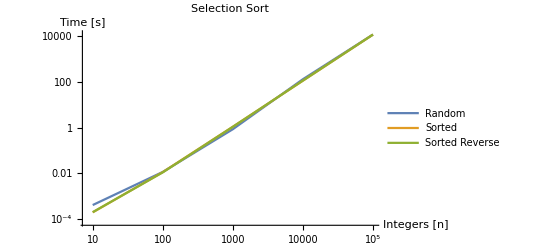

```mathematica
SelectionSortGraf = ListLogLogPlot[{
{{10, resultsSelection[[1]]},
{100, resultsSelection[[2]]},
{1000, resultsSelection[[3]]},
{10000, resultsSelection[[4]]},
{100000, resultsSelection[[5]]}},
{{10, resultsSelectionSorted[[1]]},
{100, resultsSelectionSorted[[2]]},
{1000, resultsSelectionSorted[[3]]},
{10000, resultsSelectionSorted[[4]]},
{100000, resultsSelectionSorted[[5]]}},
{{10, resultsSelectionReverse[[1]]},
{100, resultsSelectionReverse[[2]]},
{1000, resultsSelectionReverse[[3]]},
{10000, resultsSelectionReverse[[4]]},
{100000, resultsSelectionReverse[[5]]}}},
Joined->True,
PlotLabel-> "Selection Sort",
PlotLegends->{"Random", "Sorted", "Sorted Reverse"},
AxesLabel->{"Integers [n]", "Time [s]"}]
```

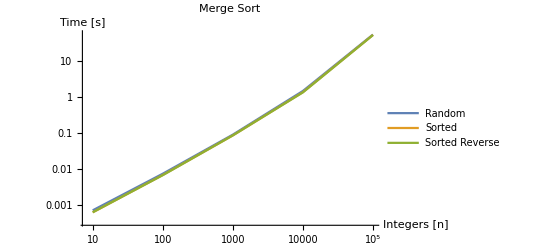

```mathematica
MergeSortGraf = ListLogLogPlot[{
{{10, resultsMerge[[1]]},
{100, resultsMerge[[2]]},
{1000, resultsMerge[[3]]},
{10000, resultsMerge[[4]]},
{100000, resultsMerge[[5]]}},
{{10, resultsMergeSorted[[1]]},
{100, resultsMergeSorted[[2]]},
{1000, resultsMergeSorted[[3]]},
{10000, resultsMergeSorted[[4]]},
{100000, resultsMergeSorted[[5]]}},
{{10, resultsMergeReverse[[1]]},
{100, resultsMergeReverse[[2]]},
{1000, resultsMergeReverse[[3]]},
{10000, resultsMergeReverse[[4]]},
{100000, resultsMergeReverse[[5]]}}},
Joined->True,
PlotLabel-> "Merge Sort",
PlotLegends->{"Random", "Sorted", "Sorted Reverse"},
AxesLabel->{"Integers [n]", "Time [s]"}]
```

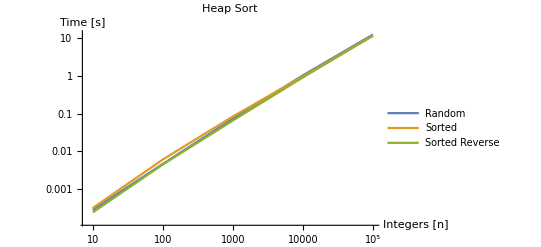

```mathematica
HeapSortGraf = ListLogLogPlot[{
{{10, resultsHeap[[1]]},
{100, resultsHeap[[2]]},
{1000, resultsHeap[[3]]},
{10000, resultsHeap[[4]]},
{100000, resultsHeap[[5]]}},
{{10, resultsHeapSorted[[1]]},
{100, resultsHeapSorted[[2]]},
{1000, resultsHeapSorted[[3]]},
{10000, resultsHeapSorted[[4]]},
{100000, resultsHeapSorted[[5]]}},
{{10, resultsHeapReverse[[1]]},
{100, resultsHeapReverse[[2]]},
{1000, resultsHeapReverse[[3]]},
{10000, resultsHeapReverse[[4]]},
{100000, resultsHeapReverse[[5]]}}},
Joined->True,
PlotLabel-> "Heap Sort",
PlotLegends->{"Random", "Sorted", "Sorted Reverse"},
AxesLabel->{"Integers [n]", "Time [s]"}]
```

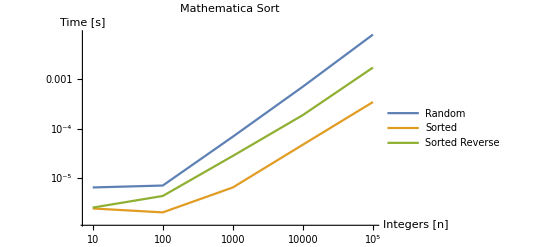

```mathematica
SortGraf = ListLogLogPlot[{
{{10, resultsSort[[1]]},
{100, resultsSort[[2]]},
{1000, resultsSort[[3]]},
{10000, resultsSort[[4]]},
{100000, resultsSort[[5]]}},
{{10, resultsSortSorted[[1]]},
{100, resultsSortSorted[[2]]},
{1000, resultsSortSorted[[3]]},
{10000, resultsSortSorted[[4]]},
{100000, resultsSortSorted[[5]]}},
{{10,resultsSortReverse[[1]]},
{100, resultsSortReverse[[2]]},
{1000, resultsSortReverse[[3]]},
{10000, resultsSortReverse[[4]]},
{100000, resultsSortReverse[[5]]}}},
Joined->True,
PlotLabel-> "Mathematica Sort",
PlotLegends->{"Random", "Sorted", "Sorted Reverse"},
AxesLabel->{"Integers [n]", "Time [s]"}]
```

```mathematica
MEGAGraf = ListLogLogPlot[
{
{{10, resultsSelection[[1]]},
{100, resultsSelection[[2]]},
{1000, resultsSelection[[3]]},
{10000, resultsSelection[[4]]},
{100000, resultsSelection[[5]]}},
{{10, resultsMerge[[1]]},
{100, resultsMerge[[2]]},
{1000, resultsMerge[[3]]},
{10000, resultsMerge[[4]]},
{100000, resultsMerge[[5]]}},
{{10, resultsHeap[[1]]},
{100, resultsHeap[[2]]},
{1000, resultsHeap[[3]]},
{10000, resultsHeap[[4]]},
{100000, resultsHeap[[5]]}},
{{10, resultsSort[[1]]},
{100, resultsSort[[2]]},
{1000, resultsSort[[3]]},
{10000, resultsSort[[4]]},
{100000, resultsSort[[5]]}},
{{10, resultsSelectionSorted[[1]]},
{100, resultsSelectionSorted[[2]]},
{1000, resultsSelectionSorted[[3]]},
{10000, resultsSelectionSorted[[4]]},
{100000, resultsSelectionSorted[[5]]}},
{{10, resultsMergeSorted[[1]]},
{100, resultsMergeSorted[[2]]},
{1000, resultsMergeSorted[[3]]},
{10000, resultsMergeSorted[[4]]},
{100000, resultsMergeSorted[[5]]}},
{{10, resultsHeapSorted[[1]]},
{100, resultsHeapSorted[[2]]},
{1000, resultsHeapSorted[[3]]},
{10000, resultsHeapSorted[[4]]},
{100000, resultsHeapSorted[[5]]}},
{{10, resultsSortSorted[[1]]},
{100, resultsSortSorted[[2]]},
{1000, resultsSortSorted[[3]]},
{10000, resultsSortSorted[[4]]},
{100000, resultsSortSorted[[5]]}},
{{10, resultsSelectionReverse[[1]]},
{100, resultsSelectionReverse[[2]]},
{1000, resultsSelectionReverse[[3]]},
{10000, resultsSelectionReverse[[4]]},
{100000, resultsSelectionReverse[[5]]}},
{{10, resultsMergeReverse[[1]]},
{100, resultsMergeReverse[[2]]},
{1000, resultsMergeReverse[[3]]},
{10000, resultsMergeReverse[[4]]},
{100000, resultsMergeReverse[[5]]}},
{{10, resultsHeapReverse[[1]]},
{100, resultsHeapReverse[[2]]},
{1000, resultsHeapReverse[[3]]},
{10000, resultsHeapReverse[[4]]},
{100000, resultsHeapReverse[[5]]}},
{{10,resultsSortReverse[[1]]},
{100, resultsSortReverse[[2]]},
{1000, resultsSortReverse[[3]]},
{10000, resultsSortReverse[[4]]},
{100000, resultsSortReverse[[5]]}}
},
Joined->True,
PlotLabel-> "MEGA graf", 
PlotLegends-> Placed[
{
"Random - Selection Sort", "Random - Merge Sort", "Random - Heap Sort", "Random - Sort", "Sorted - Selection Sort", "Sorted - Merge Sort","Sorted - Heap Sort","Sorted - Sort","Sorted Reverse - Selection Sort","Sorted Reverse - Merge Sort","Sorted Reverse - Heap Sort","Sorted Reverse - Sort"
}, Below],
AxesLabel->{"Integers [n]", "Time [s]"}]
```

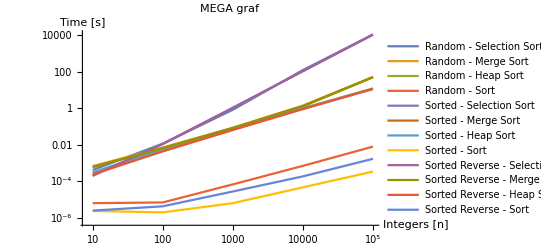

```mathematica
(* Kombinace všech výsledků *)
```

Závěr

Pro tenhle úkol jsem zvolil 3 algoritmy -> n^2 - Selection Sort, n*log(n) - Heap Sort, Merge Sort. Vyjíma Mathematica Sort, jde z grafů a tabulek vyčíst, že nejrychlejší algoritmus pro třídění byl průměrně Heap Sort. Merge Sort byl druhý a nejhůře (okolo 9 hodin...) na tom byl Selection Sort. Z tabulek i grafů jde také vyčíst, že seřazené (a reverse) pole nemají takový vliv na rychlost Selection/Heap/Merge sortů, zrychlují je pouze o malou procentuální část. Tato pole mají však kladný vliv na rychlost výpočtu vestavěné funkce Mathematica - Sort. Algoritmy s časovou složitostí n^2 nejsou však obecně k zahození. Páč jak jde vidět v MEGAgrafu (kombinace všech výsledků), Selection Sort má výhodu pro menší počet prvků! (<100).